Let us call the Olsson.wl package.

```mathematica
<<Olsson_new.wl
```

Olsson.wl v1.1
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

ROC2.wl v1.1
Authors : B. Ananthanarayan, Souvik Bera, S. Friot & Tanay Pathak

## Block 1 : Derivation of ACs around (1,0) and (0,1)

### Derivation of the first AC around (1,0) :

We define the Appell F_4 function below. Here m and n are summation indices. We’ll work with the summand only.

```mathematica
Subscript[F4AC, 1][a_,b_,c_,d_,x_,y_,m_,n_] = (Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!);
```

Appell F_4 is defined in √Abs[x]+√Abs[y]<1. We can also obtain the region of convergence (ROC) using the callroc command of Olsson.wl

```mathematica
callroc[{m,n},(Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!)]//FullSimplify
```

{{{{m+n,m+n},{m,n}},{x,y}}}

{√Abs[x]+√Abs[y]<1}

Lets store the roc below.

```mathematica
Subscript[F4ROC, 1][x_,y_]=√Abs[x]+√Abs[y]<1;
```

We now find the analytic continuations (AC) of Appell F_4 one by one. It is important to note that the Appell F_4 is symmetric under the exchange c<-> d && x<-> y. We’ll use this symmetry relation extensively.

Lets start by taking summation of m index in F_4  and writing it in terms of _2 F_1,

```mathematica
Olsson[1,{m,n},(Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!),sum-> True]
```

(y^n HypergeometricPFQ[{a+n,b+n},{c},x] Pochhammer[a,n] Pochhammer[b,n])/(n! Pochhammer[d,n])

Now we can use the AC of _2 F_1 around x=1 to find the ac of F_4 around (1,0)

```mathematica
Olsson[1,{m,n},(Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!),sum-> True,one-> True,sim-> True,roc-> True]
```

{{{{m+n,m+n,n,n},{m+2 n,n}},{1-x,y}},{{{n,n,m-n,m-n},{m-2 n,n}},{1-x,y/(-1+x)^2}}}

{√Abs[1-x]<1&&√Abs[y]<2&&(1+√(1-Abs[1-x])>√Abs[y]||√(1-Abs[1-x])+√Abs[y]<1||(√(1-Abs[1-x])+√Abs[y]>1&&√Abs[y]≤1))&&Abs[1-x]<1&&√Abs[y/(-1+x)^2]<(-1+√(1+Abs[1-x]))/Abs[1-x]&&Abs[y/(-1+x)^2]<1/4,((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n])+((1-x)^(-a-b+c+m-2 n) y^n Gamma[a+b-c] Gamma[c] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n] Pochhammer[-a+c,m-n] Pochhammer[-b+c,m-n])/(m! n! Gamma[a] Gamma[b] Pochhammer[1-a-b+c,m-2 n] Pochhammer[d,n])}

Here the option one→ True  performs the analytic continuation of _2 F_1 around x=1. The option sim→ True simplifies the Gamma functions and roc→ True  command finds the common region of convergence of the resulting two series.

The above output is a list containing two entries. The second entry is the expression of the ac of F_4 around (1,0) and the first entry is the corresponding ROC of that AC.

Lets store this AC and its ROC as F4AC_2 and F4ROC_2

```mathematica
Subscript[F4AC, 2][a_,b_,c_,d_,x_,y_,m_,n_] = ((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n])+((1-x)^(-a-b+c+m-2 n) y^n Gamma[a+b-c] Gamma[c] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n] Pochhammer[-a+c,m-n] Pochhammer[-b+c,m-n])/(m! n! Gamma[a] Gamma[b] Pochhammer[1-a-b+c,m-2 n] Pochhammer[d,n]);
```

```mathematica
Subscript[F4ROC, 2][x_,y_]=√Abs[1-x]<1&&√Abs[y]<2&&(1+√(1-Abs[1-x])>√Abs[y]||√(1-Abs[1-x])+√Abs[y]<1||(√(1-Abs[1-x])+√Abs[y]>1&&√Abs[y]≤1))&&Abs[1-x]<1&&√Abs[y/(-1+x)^2]<(-1+√(1+Abs[1-x]))/Abs[1-x]&&Abs[y/(-1+x)^2]<1/4;
```

We plot the ROCs of F4ac_1 and F4ac_2 for real values of x,y

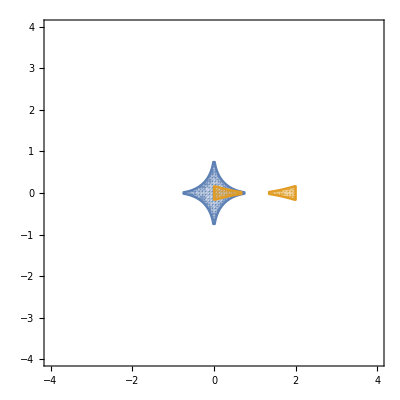

```mathematica
RegionPlot[{Subscript[F4ROC, 1][x,y],Subscript[F4ROC, 2][x,y]},{x,-4,4},{y,-4,4},PlotPoints->100]
```

### Derivation of the first AC around (0,1) :

Now the symmetry relation of F_4 can be used to find the ac around (0,1)

```mathematica
Subscript[F4AC, 2][a,b,d,c,y,x,n,m]
```

(x^m (1-y)^n Gamma[d] Gamma[-a-b+d] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-d,m] Pochhammer[1+b-d,m])/(m! n! Gamma[-a+d] Gamma[-b+d] Pochhammer[c,m] Pochhammer[1+a+b-d,2 m+n])+(x^m (1-y)^(-a-b+d-2 m+n) Gamma[a+b-d] Gamma[d] Pochhammer[1+a-d,m] Pochhammer[1+b-d,m] Pochhammer[-a+d,-m+n] Pochhammer[-b+d,-m+n])/(m! n! Gamma[a] Gamma[b] Pochhammer[c,m] Pochhammer[1-a-b+d,-2 m+n])

Let us denote this first AC around (0,1) as F4AC_3 and its ROC as F4ROC_3

```mathematica
Subscript[F4AC, 3][a_,b_,c_,d_,x_,y_,m_,n_] =(x^m (1-y)^n Gamma[d] Gamma[-a-b+d] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-d,m] Pochhammer[1+b-d,m])/(m! n! Gamma[-a+d] Gamma[-b+d] Pochhammer[c,m] Pochhammer[1+a+b-d,2 m+n])+(x^m (1-y)^(-a-b+d-2 m+n) Gamma[a+b-d] Gamma[d] Pochhammer[1+a-d,m] Pochhammer[1+b-d,m] Pochhammer[-a+d,-m+n] Pochhammer[-b+d,-m+n])/(m! n! Gamma[a] Gamma[b] Pochhammer[c,m] Pochhammer[1-a-b+d,-2 m+n]);
```

```mathematica
Subscript[F4ROC, 2][y,x]
```

√Abs[1-y]<1&&√Abs[x]<2&&(1+√(1-Abs[1-y])>√Abs[x]||√Abs[x]+√(1-Abs[1-y])<1||(√Abs[x]+√(1-Abs[1-y])>1&&√Abs[x]≤1))&&Abs[1-y]<1&&√Abs[x/(-1+y)^2]<(-1+√(1+Abs[1-y]))/Abs[1-y]&&Abs[x/(-1+y)^2]<1/4

```mathematica
Subscript[F4ROC, 3][x_,y_]=√Abs[1-y]<1&&√Abs[x]<2&&(1+√(1-Abs[1-y])>√Abs[x]||√Abs[x]+√(1-Abs[1-y])<1||(√Abs[x]+√(1-Abs[1-y])>1&&√Abs[x]≤1))&&Abs[1-y]<1&&√Abs[x/(-1+y)^2]<(-1+√(1+Abs[1-y]))/Abs[1-y]&&Abs[x/(-1+y)^2]<1/4;
```

### Derivation of the second AC around (1,0) :

The first AC around (1,0) is sum of two series. Let us denote those by V1 and V2

```mathematica
{V1,V2}=List@@Subscript[F4AC, 2][a,b,c,d,x,y,m,n]
```

{((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n]),((1-x)^(-a-b+c+m-2 n) y^n Gamma[a+b-c] Gamma[c] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n] Pochhammer[-a+c,m-n] Pochhammer[-b+c,m-n])/(m! n! Gamma[a] Gamma[b] Pochhammer[1-a-b+c,m-2 n] Pochhammer[d,n])}

We find the ROC of each of the series

```mathematica
VROCs=Flatten[callroc[{m,n},#]&/@{V1,V2}]
```

{{{{m+n,m+n,n,n},{m+2 n,n}},{1-x,y}}}

{{{{n,n,m-n,m-n},{m-2 n,n}},{1-x,y/(-1+x)^2}}}

{√Abs[1-x]<1&&√Abs[y]<2&&(1+√(1-Abs[1-x])>√Abs[y]||√(1-Abs[1-x])+√Abs[y]<1||(√(1-Abs[1-x])+√Abs[y]>1&&√Abs[y]≤1)),Abs[1-x]<1&&√Abs[y/(-1+x)^2]<(-1+√(1+Abs[1-x]))/Abs[1-x]&&Abs[y/(-1+x)^2]<1/4}

Let us plot them for real values of x and y

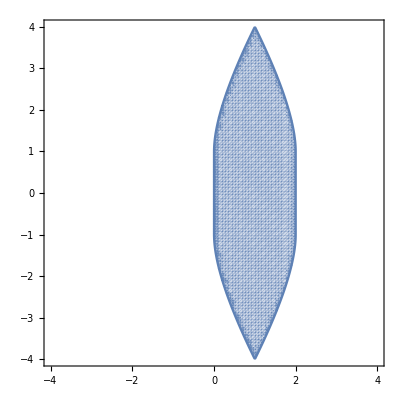
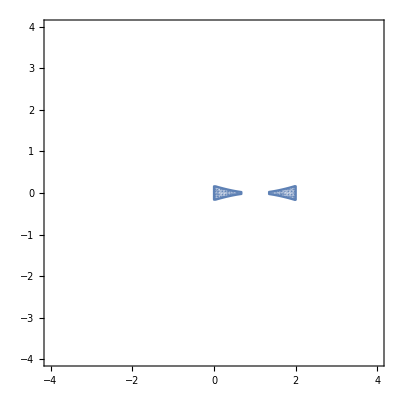

```mathematica
RegionPlot[#,{x,-4,4},{y,-4,4},PlotPoints->100]&/@VROCs
```

We observe from the ROC plot above that  V2 series can be analytically continued futher.

Taking the n-summation of V2 yield _4 F_3(z) with z =(4 y)/(1-x)^2

```mathematica
Olsson[2,{m,n},V2,sum-> True]
```

((1-x)^(-a-b+c+m) Gamma[a+b-c] Gamma[c] HypergeometricPFQ[{1+a-c,1+b-c,a/2+b/2-c/2-m/2,1/2+a/2+b/2-c/2-m/2},{d,1+a-c-m,1+b-c-m},(4 y)/(1-x)^2] Pochhammer[-a+c,m] Pochhammer[-b+c,m])/(m! Gamma[a] Gamma[b] Pochhammer[1-a-b+c,m])

Now performing the AC of _4 F_3(z) around z=∞, we find two non-vanishing series. Denoting those by V21 and V22

```mathematica
{V21,V22}=List@@(Olsson[2,{m,n},V2,inf-> True,sim-> True])
```

{(2^(-a-b-2 n) √π (2-2 x)^(c+m) (1-x)^(-a-b) ((-1+x)^2/y)^(1+n) (-y/(-1+x)^2)^(1/2 (1-a-b+c+m)) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (1+a-b-c),m/2] Pochhammer[1/2 (1-a+b-c),m/2] Pochhammer[1/2 (1+a+b-c),-m/2+n] Pochhammer[1/2 (1+a-b+c),-m/2] Pochhammer[1/2 (1+a-b+c),m/2+n] Pochhammer[1/2 (1-a+b+c),-m/2] Pochhammer[1/2 (1-a+b+c),m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-c)] Gamma[1/2 (-1-a-b+c+2 d)] Pochhammer[3/2,n] Pochhammer[1/2 (1+a-b-c),-m/2] Pochhammer[1/2 (1-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (1+a-b+c),m/2] Pochhammer[1/2 (1+a-b+c),-m/2+n] Pochhammer[1/2 (1-a+b+c),m/2] Pochhammer[1/2 (1-a+b+c),-m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2] Pochhammer[1/2 (-1-a-b+c+2 d),m/2]),(2^(-a-b+c+m-2 n) √π (1-x)^(-a-b+c+m) ((-1+x)^2/y)^n (-y/(-1+x)^2)^(1/2 (-a-b+c+m)) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (2+a-b-c),m/2] Pochhammer[1/2 (2-a+b-c),m/2] Pochhammer[1/2 (a+b-c),-m/2+n] Pochhammer[1/2 (a-b+c),-m/2] Pochhammer[1/2 (a-b+c),m/2+n] Pochhammer[1/2 (-a+b+c),-m/2] Pochhammer[1/2 (-a+b+c),m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (1+a+b-c)] Gamma[1/2 (-a-b+c+2 d)] Pochhammer[1/2,n] Pochhammer[1/2 (2+a-b-c),-m/2] Pochhammer[1/2 (2-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (a-b+c),m/2] Pochhammer[1/2 (a-b+c),-m/2+n] Pochhammer[1/2 (-a+b+c),m/2] Pochhammer[1/2 (-a+b+c),-m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2] Pochhammer[1/2 (-a-b+c+2 d),m/2])}

Thus the second AC around (1,0) is the sum of three series V1, V21 and V22

```mathematica
V1+V21+V22
```

((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n])+(2^(-a-b-2 n) √π (2-2 x)^(c+m) (1-x)^(-a-b) ((-1+x)^2/y)^(1+n) (-y/(-1+x)^2)^(1/2 (1-a-b+c+m)) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (1+a-b-c),m/2] Pochhammer[1/2 (1-a+b-c),m/2] Pochhammer[1/2 (1+a+b-c),-m/2+n] Pochhammer[1/2 (1+a-b+c),-m/2] Pochhammer[1/2 (1+a-b+c),m/2+n] Pochhammer[1/2 (1-a+b+c),-m/2] Pochhammer[1/2 (1-a+b+c),m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-c)] Gamma[1/2 (-1-a-b+c+2 d)] Pochhammer[3/2,n] Pochhammer[1/2 (1+a-b-c),-m/2] Pochhammer[1/2 (1-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (1+a-b+c),m/2] Pochhammer[1/2 (1+a-b+c),-m/2+n] Pochhammer[1/2 (1-a+b+c),m/2] Pochhammer[1/2 (1-a+b+c),-m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2] Pochhammer[1/2 (-1-a-b+c+2 d),m/2])+(2^(-a-b+c+m-2 n) √π (1-x)^(-a-b+c+m) ((-1+x)^2/y)^n (-y/(-1+x)^2)^(1/2 (-a-b+c+m)) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (2+a-b-c),m/2] Pochhammer[1/2 (2-a+b-c),m/2] Pochhammer[1/2 (a+b-c),-m/2+n] Pochhammer[1/2 (a-b+c),-m/2] Pochhammer[1/2 (a-b+c),m/2+n] Pochhammer[1/2 (-a+b+c),-m/2] Pochhammer[1/2 (-a+b+c),m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (1+a+b-c)] Gamma[1/2 (-a-b+c+2 d)] Pochhammer[1/2,n] Pochhammer[1/2 (2+a-b-c),-m/2] Pochhammer[1/2 (2-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (a-b+c),m/2] Pochhammer[1/2 (a-b+c),-m/2+n] Pochhammer[1/2 (-a+b+c),m/2] Pochhammer[1/2 (-a+b+c),-m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2] Pochhammer[1/2 (-a-b+c+2 d),m/2])

Let us denote this AC as F4AC_4

```mathematica
Subscript[F4AC, 4][a_,b_,c_,d_,x_,y_,m_,n_] =((1-x)^m y^n Gamma[c] Gamma[-a-b+c] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-c,n] Pochhammer[1+b-c,n])/(m! n! Gamma[-a+c] Gamma[-b+c] Pochhammer[1+a+b-c,m+2 n] Pochhammer[d,n])+(2^(-a-b-2 n) √π (2-2 x)^(c+m) (1-x)^(-a-b) ((-1+x)^2/y)^(1+n) (-y/(-1+x)^2)^(1/2 (1-a-b+c+m)) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (1+a-b-c),m/2] Pochhammer[1/2 (1-a+b-c),m/2] Pochhammer[1/2 (1+a+b-c),-m/2+n] Pochhammer[1/2 (1+a-b+c),-m/2] Pochhammer[1/2 (1+a-b+c),m/2+n] Pochhammer[1/2 (1-a+b+c),-m/2] Pochhammer[1/2 (1-a+b+c),m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-c)] Gamma[1/2 (-1-a-b+c+2 d)] Pochhammer[3/2,n] Pochhammer[1/2 (1+a-b-c),-m/2] Pochhammer[1/2 (1-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (1+a-b+c),m/2] Pochhammer[1/2 (1+a-b+c),-m/2+n] Pochhammer[1/2 (1-a+b+c),m/2] Pochhammer[1/2 (1-a+b+c),-m/2+n] Pochhammer[1/2 (3+a+b-c-2 d),-m/2] Pochhammer[1/2 (-1-a-b+c+2 d),m/2])+(2^(-a-b+c+m-2 n) √π (1-x)^(-a-b+c+m) ((-1+x)^2/y)^n (-y/(-1+x)^2)^(1/2 (-a-b+c+m)) Gamma[a+b-c] Gamma[c] Gamma[d] Pochhammer[1/2 (2+a-b-c),m/2] Pochhammer[1/2 (2-a+b-c),m/2] Pochhammer[1/2 (a+b-c),-m/2+n] Pochhammer[1/2 (a-b+c),-m/2] Pochhammer[1/2 (a-b+c),m/2+n] Pochhammer[1/2 (-a+b+c),-m/2] Pochhammer[1/2 (-a+b+c),m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2+n])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (1+a+b-c)] Gamma[1/2 (-a-b+c+2 d)] Pochhammer[1/2,n] Pochhammer[1/2 (2+a-b-c),-m/2] Pochhammer[1/2 (2-a+b-c),-m/2] Pochhammer[1/2 (a+b-c),-m/2] Pochhammer[1/2 (1+a+b-c),-m/2] Pochhammer[1-a-b+c,m] Pochhammer[1/2 (a-b+c),m/2] Pochhammer[1/2 (a-b+c),-m/2+n] Pochhammer[1/2 (-a+b+c),m/2] Pochhammer[1/2 (-a+b+c),-m/2+n] Pochhammer[1/2 (2+a+b-c-2 d),-m/2] Pochhammer[1/2 (-a-b+c+2 d),m/2]);
```

Next we find the ROC of each of the three series. The intersection of those ROC will be the ROC of the above AC

```mathematica
Simplify[And@@Flatten[callroc[{m,n},#]&/@{V1,V21,V22}]]
```

{{{{m+n,m+n,n,n},{m+2 n,n}},{1-x,y}}}

{{{{m/2,m/2,-m/2+n,-m/2,m/2+n,-m/2,m/2+n,-m/2+n},{n,-m/2,-m/2,-m/2,-m/2,m,m/2,-m/2+n,m/2,-m/2+n,-m/2,m/2}},{-2 (-1+x) √(-y/(-1+x)^2),(-1+x)^2/(4 y)}}}

{{{{m/2,m/2,-m/2+n,-m/2,m/2+n,-m/2,m/2+n,-m/2+n},{n,-m/2,-m/2,-m/2,-m/2,m,m/2,-m/2+n,m/2,-m/2+n,-m/2,m/2}},{-2 (-1+x) √(-y/(-1+x)^2),(-1+x)^2/(4 y)}}}

√Abs[1-x]<1&&√Abs[(-1+x)^2/y]+Abs[(-1+x) √(-y/(-1+x)^2)]<2&&Abs[(-1+x)^2/y]<4&&√Abs[y]<2&&Abs[(-1+x) √(-y/(-1+x)^2)]<2&&(√(1-Abs[1-x])+√Abs[y]<1||1+√(1-Abs[1-x])>√Abs[y]||(√(1-Abs[1-x])+√Abs[y]>1&&√Abs[y]≤1))

Let us denote it by F4ROC_4

```mathematica
Subscript[F4ROC, 4][x_,y_]=√Abs[1-x]<1&&√Abs[(-1+x)^2/y]+Abs[(-1+x) √(-y/(-1+x)^2)]<2&&Abs[(-1+x)^2/y]<4&&√Abs[y]<2&&Abs[(-1+x) √(-y/(-1+x)^2)]<2&&(√(1-Abs[1-x])+√Abs[y]<1||1+√(1-Abs[1-x])>√Abs[y]||(√(1-Abs[1-x])+√Abs[y]>1&&√Abs[y]≤1));
```

The ROC of the above series is plotted below.

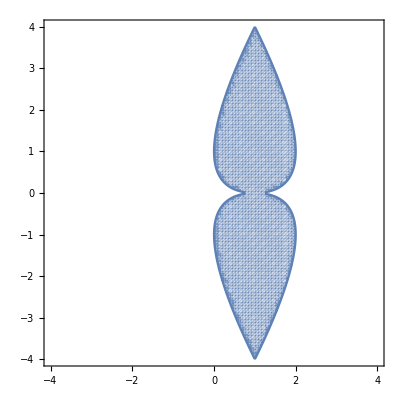

```mathematica
RegionPlot[Subscript[F4ROC, 4][x,y],{x,-4,4},{y,-4,4},PlotPoints->100]
```

### Derivation of the second AC around (0,1)

Again we use the symmetry of F_4 to find

```mathematica
Subscript[F4AC, 4][a,b,d,c,y,x,n,m]
```

(x^m (1-y)^n Gamma[d] Gamma[-a-b+d] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-d,m] Pochhammer[1+b-d,m])/(m! n! Gamma[-a+d] Gamma[-b+d] Pochhammer[c,m] Pochhammer[1+a+b-d,2 m+n])+(2^(-a-b-2 m) √π (2-2 y)^(d+n) (1-y)^(-a-b) (-x/(-1+y)^2)^(1/2 (1-a-b+d+n)) ((-1+y)^2/x)^(1+m) Gamma[c] Gamma[a+b-d] Gamma[d] Pochhammer[1/2 (1+a-b-d),n/2] Pochhammer[1/2 (1-a+b-d),n/2] Pochhammer[1/2 (1+a+b-d),m-n/2] Pochhammer[1/2 (3+a+b-2 c-d),m-n/2] Pochhammer[1/2 (1+a-b+d),m+n/2] Pochhammer[1/2 (1+a-b+d),-n/2] Pochhammer[1/2 (1-a+b+d),m+n/2] Pochhammer[1/2 (1-a+b+d),-n/2])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-d)] Gamma[1/2 (-1-a-b+2 c+d)] Pochhammer[3/2,m] Pochhammer[1/2 (1+a-b-d),-n/2] Pochhammer[1/2 (1-a+b-d),-n/2] Pochhammer[1/2 (a+b-d),-n/2] Pochhammer[1/2 (1+a+b-d),-n/2] Pochhammer[1/2 (3+a+b-2 c-d),-n/2] Pochhammer[1-a-b+d,n] Pochhammer[1/2 (1+a-b+d),m-n/2] Pochhammer[1/2 (1+a-b+d),n/2] Pochhammer[1/2 (1-a+b+d),m-n/2] Pochhammer[1/2 (1-a+b+d),n/2] Pochhammer[1/2 (-1-a-b+2 c+d),n/2])+(2^(-a-b+d-2 m+n) √π (1-y)^(-a-b+d+n) (-x/(-1+y)^2)^(1/2 (-a-b+d+n)) ((-1+y)^2/x)^m Gamma[c] Gamma[a+b-d] Gamma[d] Pochhammer[1/2 (2+a-b-d),n/2] Pochhammer[1/2 (2-a+b-d),n/2] Pochhammer[1/2 (a+b-d),m-n/2] Pochhammer[1/2 (2+a+b-2 c-d),m-n/2] Pochhammer[1/2 (a-b+d),m+n/2] Pochhammer[1/2 (a-b+d),-n/2] Pochhammer[1/2 (-a+b+d),m+n/2] Pochhammer[1/2 (-a+b+d),-n/2])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (1+a+b-d)] Gamma[1/2 (-a-b+2 c+d)] Pochhammer[1/2,m] Pochhammer[1/2 (2+a-b-d),-n/2] Pochhammer[1/2 (2-a+b-d),-n/2] Pochhammer[1/2 (a+b-d),-n/2] Pochhammer[1/2 (1+a+b-d),-n/2] Pochhammer[1/2 (2+a+b-2 c-d),-n/2] Pochhammer[1-a-b+d,n] Pochhammer[1/2 (a-b+d),m-n/2] Pochhammer[1/2 (a-b+d),n/2] Pochhammer[1/2 (-a+b+d),m-n/2] Pochhammer[1/2 (-a+b+d),n/2] Pochhammer[1/2 (-a-b+2 c+d),n/2])

```mathematica
Subscript[F4AC, 5][a_,b_,c_,d_,x_,y_,m_,n_] =(x^m (1-y)^n Gamma[d] Gamma[-a-b+d] Pochhammer[a,m+n] Pochhammer[b,m+n] Pochhammer[1+a-d,m] Pochhammer[1+b-d,m])/(m! n! Gamma[-a+d] Gamma[-b+d] Pochhammer[c,m] Pochhammer[1+a+b-d,2 m+n])+(2^(-a-b-2 m) √π (2-2 y)^(d+n) (1-y)^(-a-b) (-x/(-1+y)^2)^(1/2 (1-a-b+d+n)) ((-1+y)^2/x)^(1+m) Gamma[c] Gamma[a+b-d] Gamma[d] Pochhammer[1/2 (1+a-b-d),n/2] Pochhammer[1/2 (1-a+b-d),n/2] Pochhammer[1/2 (1+a+b-d),m-n/2] Pochhammer[1/2 (3+a+b-2 c-d),m-n/2] Pochhammer[1/2 (1+a-b+d),m+n/2] Pochhammer[1/2 (1+a-b+d),-n/2] Pochhammer[1/2 (1-a+b+d),m+n/2] Pochhammer[1/2 (1-a+b+d),-n/2])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (a+b-d)] Gamma[1/2 (-1-a-b+2 c+d)] Pochhammer[3/2,m] Pochhammer[1/2 (1+a-b-d),-n/2] Pochhammer[1/2 (1-a+b-d),-n/2] Pochhammer[1/2 (a+b-d),-n/2] Pochhammer[1/2 (1+a+b-d),-n/2] Pochhammer[1/2 (3+a+b-2 c-d),-n/2] Pochhammer[1-a-b+d,n] Pochhammer[1/2 (1+a-b+d),m-n/2] Pochhammer[1/2 (1+a-b+d),n/2] Pochhammer[1/2 (1-a+b+d),m-n/2] Pochhammer[1/2 (1-a+b+d),n/2] Pochhammer[1/2 (-1-a-b+2 c+d),n/2])+(2^(-a-b+d-2 m+n) √π (1-y)^(-a-b+d+n) (-x/(-1+y)^2)^(1/2 (-a-b+d+n)) ((-1+y)^2/x)^m Gamma[c] Gamma[a+b-d] Gamma[d] Pochhammer[1/2 (2+a-b-d),n/2] Pochhammer[1/2 (2-a+b-d),n/2] Pochhammer[1/2 (a+b-d),m-n/2] Pochhammer[1/2 (2+a+b-2 c-d),m-n/2] Pochhammer[1/2 (a-b+d),m+n/2] Pochhammer[1/2 (a-b+d),-n/2] Pochhammer[1/2 (-a+b+d),m+n/2] Pochhammer[1/2 (-a+b+d),-n/2])/(m! n! Gamma[a] Gamma[b] Gamma[1/2 (1+a+b-d)] Gamma[1/2 (-a-b+2 c+d)] Pochhammer[1/2,m] Pochhammer[1/2 (2+a-b-d),-n/2] Pochhammer[1/2 (2-a+b-d),-n/2] Pochhammer[1/2 (a+b-d),-n/2] Pochhammer[1/2 (1+a+b-d),-n/2] Pochhammer[1/2 (2+a+b-2 c-d),-n/2] Pochhammer[1-a-b+d,n] Pochhammer[1/2 (a-b+d),m-n/2] Pochhammer[1/2 (a-b+d),n/2] Pochhammer[1/2 (-a+b+d),m-n/2] Pochhammer[1/2 (-a+b+d),n/2] Pochhammer[1/2 (-a-b+2 c+d),n/2]);
```

and

```mathematica
Subscript[F4ROC, 4][y,x]
```

√Abs[1-y]<1&&Abs[√(-x/(-1+y)^2) (-1+y)]+√Abs[(-1+y)^2/x]<2&&Abs[(-1+y)^2/x]<4&&√Abs[x]<2&&Abs[√(-x/(-1+y)^2) (-1+y)]<2&&(√Abs[x]+√(1-Abs[1-y])<1||1+√(1-Abs[1-y])>√Abs[x]||(√Abs[x]+√(1-Abs[1-y])>1&&√Abs[x]≤1))

```mathematica
Subscript[F4ROC, 5][x_,y_]=√Abs[1-y]<1&&Abs[√(-x/(-1+y)^2) (-1+y)]+√Abs[(-1+y)^2/x]<2&&Abs[(-1+y)^2/x]<4&&√Abs[x]<2&&Abs[√(-x/(-1+y)^2) (-1+y)]<2&&(√Abs[x]+√(1-Abs[1-y])<1||1+√(1-Abs[1-y])>√Abs[x]||(√Abs[x]+√(1-Abs[1-y])>1&&√Abs[x]≤1));
```

## Block 2 : Derivation of the AC around (∞,0) and (0,∞)

### Derivation of AC around (∞,0)

We now go on to find the ac of F_4 around (∞,0). Starting from the definition of the F_4 and summing over the index m, we find

```mathematica
Olsson[1,{m,n},(Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!),sum-> True]
```

(y^n HypergeometricPFQ[{a+n,b+n},{c},x] Pochhammer[a,n] Pochhammer[b,n])/(n! Pochhammer[d,n])

Now using the AC of _2 F_1(x) around x=∞, we find the AC of F_4 around (∞,0)

```mathematica
Olsson[1,{m,n},(Pochhammer[a,m+n]Pochhammer[b,m+n])/(Pochhammer[c,m]Pochhammer[d,n])x^m/(m!)y^n/(n!),inf-> True,sim-> True,roc-> True]
```

{{{{m+n,m+n},{m,n}},{1/x,y/x}}}

{1/Abs[x]<1&&√Abs[y/x]<1-1/(√Abs[x])&&Abs[y/x]<1,((-1)^n (-x)^(-a-n) x^-m y^n Gamma[-a+b] Gamma[c] Pochhammer[a,m+n] Pochhammer[1+a-c,m+n])/(m! n! Gamma[b] Gamma[-a+c] Pochhammer[1+a-b,m] Pochhammer[d,n])+((-1)^n (-x)^(-b-n) x^-m y^n Gamma[a-b] Gamma[c] Pochhammer[b,m+n] Pochhammer[1+b-c,m+n])/(m! n! Gamma[a] Gamma[-b+c] Pochhammer[1-a+b,m] Pochhammer[d,n])}

Lets store them as

```mathematica
Subscript[F4AC, 6][a_,b_,c_,d_,x_,y_,m_,n_] = ((-1)^n (-x)^(-a-n) x^-m y^n Gamma[-a+b] Gamma[c] Pochhammer[a,m+n] Pochhammer[1+a-c,m+n])/(m! n! Gamma[b] Gamma[-a+c] Pochhammer[1+a-b,m] Pochhammer[d,n])+((-1)^n (-x)^(-b-n) x^-m y^n Gamma[a-b] Gamma[c] Pochhammer[b,m+n] Pochhammer[1+b-c,m+n])/(m! n! Gamma[a] Gamma[-b+c] Pochhammer[1-a+b,m] Pochhammer[d,n]);
```

```mathematica
Subscript[F4ROC, 6][x_,y_]=1/Abs[x]<1&&√Abs[y/x]<1-1/(√Abs[x])&&Abs[y/x]<1;
```

### Derivation of the AC around (0,∞) :

Using symmetry we find its mirror ac

```mathematica
Subscript[F4AC, 6][a,b,d,c,y,x,n,m]
```

((-1)^m x^m (-y)^(-a-m) y^-n Gamma[-a+b] Gamma[d] Pochhammer[a,m+n] Pochhammer[1+a-d,m+n])/(m! n! Gamma[b] Gamma[-a+d] Pochhammer[1+a-b,n] Pochhammer[c,m])+((-1)^m x^m (-y)^(-b-m) y^-n Gamma[a-b] Gamma[d] Pochhammer[b,m+n] Pochhammer[1+b-d,m+n])/(m! n! Gamma[a] Gamma[-b+d] Pochhammer[1-a+b,n] Pochhammer[c,m])

```mathematica
Subscript[F4AC, 7][a_,b_,c_,d_,x_,y_,m_,n_] =((-1)^m x^m (-y)^(-a-m) y^-n Gamma[-a+b] Gamma[d] Pochhammer[a,m+n] Pochhammer[1+a-d,m+n])/(m! n! Gamma[b] Gamma[-a+d] Pochhammer[1+a-b,n] Pochhammer[c,m])+((-1)^m x^m (-y)^(-b-m) y^-n Gamma[a-b] Gamma[d] Pochhammer[b,m+n] Pochhammer[1+b-d,m+n])/(m! n! Gamma[a] Gamma[-b+d] Pochhammer[1-a+b,n] Pochhammer[c,m]);
```

```mathematica
Subscript[F4ROC, 6][y,x]
```

1/Abs[y]<1&&√Abs[x/y]<1-1/(√Abs[y])&&Abs[x/y]<1

```mathematica
Subscript[F4ROC, 7][x_,y_]=1/Abs[y]<1&&√Abs[x/y]<1-1/(√Abs[y])&&Abs[x/y]<1;
```

## Plot of all the ROCs

We plot all the seven ROCs together.

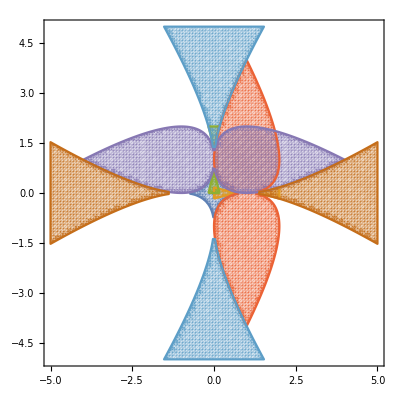

```mathematica
RegionPlot[{Subscript[F4ROC, 1][x,y],Subscript[F4ROC, 2][x,y],Subscript[F4ROC, 3][x,y],Subscript[F4ROC, 4][x,y],Subscript[F4ROC, 5][x,y],Subscript[F4ROC, 6][x,y],Subscript[F4ROC, 7][x,y]},{x,-5,5},{y,-5,5},PlotPoints->100]
```